```mathematica
ClearAll[n,kT, χ,  eInt, sInt, r, d, phit, M, poArr, piArr, pAverArr, xArr, nMax]
Clear[j]
```

## Class I

```mathematica
(* Max assembly size*)
M=15;
r=1;

(* Total monomer mass *)
phit=0.3;

(*phit=0.5;*)
(*phit=0.35;*)


kT=0.45;

(* Internal free energies *)
eInt= -1;
sInt=-2.; 

(* dimension of assebies d=1 -> linear *)
d=1;


dt= 0.01;
nIter = 2000;

(* interaction assemblies solvent *)
χ=1/kT;
```

```mathematica
(***************************** MONOMER PICKUP**************************************)
(*delrChem is a M vector, with i-th component containing the fluxes from the i to the i+1 assembly associated to the single reactions. The last element is set to 0, since there is no flux to M+1 mers*)

(* d=1, class 1 *)
(*delrChem = Join[Table[  (phi[i]*phi[1])/i *Exp[1-(eInt/kT-sInt )]-phi[i+1]/(i+1),{i,1,M-1}]  ,{0}];*)

(*rChem is a M+1 vector, with the net vol fraction variations coming from ALL CHEMICAL REACTIONS. The last element is the change in water,  set to 0. *)
(*rChem = Join[{-delrChem[[1]]-Sum[ delrChem[[i]],{i,1,M-1}]}, Table[-i delrChem[[i]]+i delrChem[[i-1]],{i,2,M}],{0}];*)


(***************************** AGG AND FRAG **************************************)
ϕSt = E^(eInt/kT-sInt - 1);

(*delrChem is a M vector, with i-th component containing the fluxes from the i to the i+1 assembly associated to the single reactions. The last element is set to 0, since there is no flux to M+1 mers*)

(* d=1, class 1 *)
delrChem = Join[Table[Table[  2(phi[i]*phi[j])/(i*j)-2 phi[i+j]/(i+j) ϕSt,{j,1,M-1}]  ,{i,1,M-1}],{0}];

(*rChem is a M+1 vector, with the net vol fraction variations coming from ALL CHEMICAL REACTIONS. The last element is the change in water,  set to 0. *)
rChem = Join[ Table[i (1/2 Sum[delrChem[[j,i-j]],{j,1,i-1}] - Sum[delrChem[[i,j]],{j,1,M-i}]),{i,1,M}],{0}];
 


(* TO DETERMINE THE DIFFUSIVE CURRENTS! *)

(*Sgam = Sum[ phi[i]/i,{i,1,M} ]+ (1-Sum[ phi[i],{i,1,M} ])+χ Sum[ phi[i],{i,1,M} ](1-Sum[ phi[i],{i,1,M} ]);*)
(* with phi[M+1] = 1-sum... *)
(*gami = Table[   Exp[i( χ(1-Sum[ phi[i],{i,1,M} ])^2- Sum[ phi[i]/i,{i,1,M} ]- (1-Sum[ phi[i],{i,1,M} ])) ],{i,1,M}];
gamM1 =  Exp[    χ (Sum[ phi[i],{i,1,M} ])^2- Sum[ phi[i]/i,{i,1,M} ]- (1-Sum[ phi[i],{i,1,M} ]) ];*)

(*ACTIVITIES OF ASSEMBLIES OF SIZE i*)
gami = Table[   Exp[i( χ( phi[M+1])^2- Sum[ phi[k]/k,{k,1,M} ]-  phi[M+1]) ],{i,1,M}];
(*ACTIVITIES OF SOLVENT (M+1)-component *)
gamM1 =  Exp[    χ ( 1-phi[M+1])^2- Sum[ phi[k]/k,{k,1,M} ]-  phi[M+1] ]; 

gam = Simplify[Join[gami,{gamM1}]];


phidot = Table[ rChem[[i]]-j[i]+phi[i]Sum[  j[k], {k,1,M+1}], {i,1,M+1}];

(* quantities to equate to impose phase equilibrium *)
eqForj =Table[  gam [[i]]* phidot[[i]] +phi[i] Sum[D[gam[[i]],phi[k] ]*phidot[[k]] ,{ k,1,M+1}] ,{i,1,M+1}];
```

## Evolution of a homogeneous state

```mathematica
pAver = Join[{phit},Table[0,{i,1,M-1}],{1-phit}];

pHomo = {pAver};

For[k=0,k<nIter-1,k++,

incre = rChem/.Table[phi[i]->pAver[[i]],{i,1,M+1}];
(*Print[Sum[incre[[i]]*i,{i,1,M+1}]];*)
pAver = pAver+ dt* incre;
AppendTo[pHomo,pAver] ;

]
```

This should be 1

1.

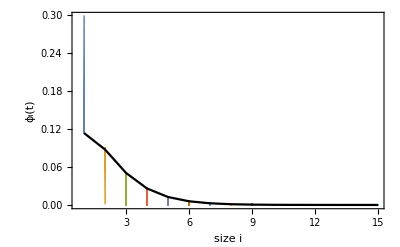

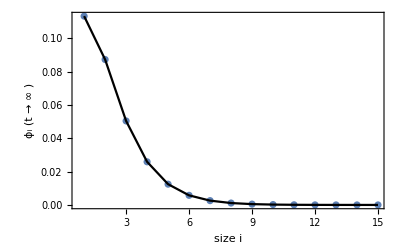

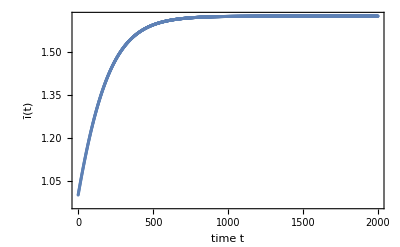

```mathematica
pHomoFinal = pHomo[[-1]];

Print["This should be 1"]
Sum[pHomoFinal[[i]],{i,1,M+1}]
pHomo = (MatrixForm[pHomo])[[1]] ;

SetDirectory[NotebookDirectory[]];
pnHomoEq=Flatten[Import["results/stat_states/classI_pn_homo.csv"]];
(*Export["./../results/kin_I/TEST_homo.csv",Take[nHomo, -nIter] ];*)
plHomo = ListPlot[  Table[ Table[{j,pHomo[[i,j]]},{i,2,Length[pHomo]} ],{j,1,M}], PlotRange->All ];
plHomoLast = ListPlot[  Table[ {j,pHomo[[-1,j]]},{j,1,M}], PlotRange->All ];
plHomoEq = ListLinePlot[  pnHomoEq, PlotRange->All , PlotStyle->Black];
Show[plHomo, plHomoEq,Frame->True, FrameLabel->{"size i", "ϕ_i(t)"}]
Show[plHomoLast, plHomoEq, Frame->True, FrameLabel->{"size i", "ϕ_i (t → ∞ )"}]

meanhomo = Table[ Sum[pHomo[[i,k]],{k,1,M}]/Sum[pHomo[[i,k]]/k,{k,1,M}],{i,1,nIter}];
ListPlot[ meanhomo, PlotRange->All, Frame->True, FrameLabel->{"time t", " ī(t)"}]
```

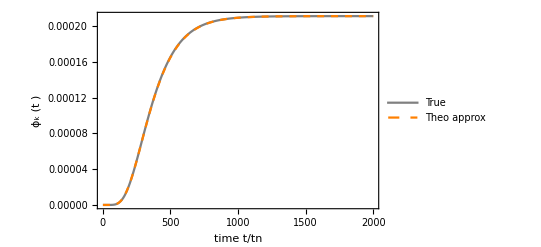

```mathematica
(*ϕSt = E^(eInt/kT-sInt - (1-phi)(χ- χp)/kT - 1)*)
ϕSt = E^(eInt/kT-sInt - 1);

bet = (1+2 phit/ϕSt-√(1+4 phit/ϕSt))/(2 phit/ϕSt);
alp = 1/bet;

at = (1-E^(-(alp - bet)ntime*dt*phit))/(alp -bet E^(-(alp - bet)ntime*dt*phit));

ktest = 10;
pkTheo = Table[( ktest(1-at)^2 at^(ktest-1) phi )/.{phi->phit},{ntime,0,nIter-2}];
pltestTheo = ListLinePlot[ { pHomo[[;;,ktest]], pkTheo} ,PlotStyle->{{Gray,Thick}, {Orange, Dashed}},PlotLegends->{"True", "Theo approx"},PlotRange->All, Frame->True, FrameLabel->{"time t/tn", " ϕ_k (t )"}]
```

## Evolution of a phase separated state

```mathematica
(* Phase separation with just monomers, initial condition *)
f1=phi Log[phi] + (1- phi)  Log[1-  phi] + χ*phi (1-phi);

mu1 = D[f1,phi];
osmP1 = Simplify[f1 -   D[freeM,phi]*phi];

eqs1={  (mu1/.phi->pI)==(mu1/.phi->pII ), (osmP1/.phi->pI)==(osmP1/.phi->pII )};

dilGuess = 0.1;
initial={{pI,1-dilGuess},{pII,dilGuess}};

sol1 = FindRoot[eqs1,initial];


phiI0 =Join[ {pI/.sol1}, Table[0,{i,1,M-1}],{1-pI/.sol1} ]
phiII0 =Join[ {pII/.sol1}, Table[0,{i,1,M-1}],{1-pII/.sol1} ]
VI0=( phit-(pII/.sol1))/((pI/.sol1)-(pII/.sol1))
```

{0.762715,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.237285}

{0.237285,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.762715}

0.119359

```mathematica
phiIArr = {phiI0};
phiIIArr = {phiII0};
VIArr = {VI0} ;

phiI =phiI0;
phiII =phiII0;
x =VI0;

For[k=0,k<nIter-1,k++,


(*Replacement tables, I-> dense phase, II-> dilute phase*)
repI = Table[phi[i]->phiI[[i]],{i,1,M+1}];
repII = Join[Table[phi[i]->phiII[[i]],{i,1,M+1}],Table[j[i]->j[i]/(1-1/x),{i,1,M+1}]];

(* DETERMINING DIFFUSIVE CURRENTS *)
eqs = Table[(eqForj[[i]]/.repI)-(eqForj[[i]]/.repII)==0 ,{i,1,M+1}];

coef = Normal[CoefficientArrays[eqs,Table[j[i],{i,1,M+1}]]];
const = -coef[[1]];
equaMat = coef[[2]];

(* SOLUTION FOR THE CURRENTS *)
jsol=LinearSolve[equaMat, const];


repSol = Table[j[i]->(jsol[[i]]), {i,1,M+1}];


increI = phidot/.repI/.repSol;
increII = phidot/.repII/.repSol;
increx = (-x * Sum[j[i],{i,1,M+1}])/.repSol;

(* EULER STEP *)
phiI = phiI+ dt* increI;
AppendTo[phiIArr,phiI] ;

phiII = phiII+ dt* increII;
AppendTo[phiIIArr,phiII] ;

x = x+ dt*increx;
AppendTo[VIArr,x] ;

]
```

NO NEGATIVE NUMBERS

This should be 1: 1.

This should be 1: 1.

INSIDE

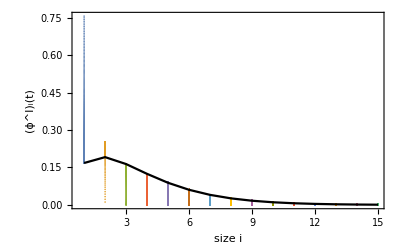

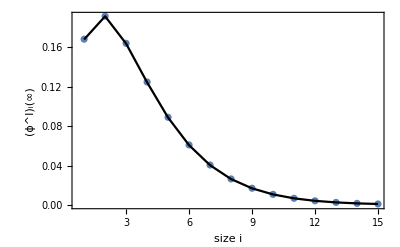

OUTSIDE

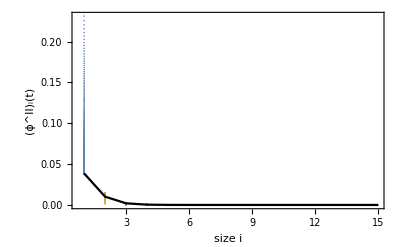

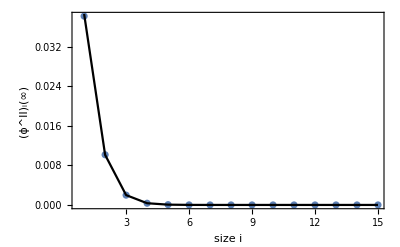

```mathematica
phiIArr = (MatrixForm[phiIArr])[[1]] ;
phiIIArr = (MatrixForm[phiIIArr])[[1]]; 
phiAverArr = Table[phiIIArr[[i]]*(1-VIArr[[i]])+ phiIArr[[i]]*VIArr[[i]],{i,1,Length[VIArr]}];
If[Min[phiIArr]<-10^-8|| Min[phiIIArr]<-10^-8,Print["AHI CARRAMBA"],Print["NO NEGATIVE NUMBERS "] ];

phiIfinal = phiIArr[[-1]];
Print["This should be 1: ", Sum[phiIfinal[[i]],{i,1,M+1}]];


phiIIfinal = phiIIArr[[-1]];
Print["This should be 1: ", Sum[phiIIfinal[[i]],{i,1,M+1}] ]

pnIEq=Flatten[Import["results/stat_states/classI_pn_in.csv"]];
pnIIEq=Flatten[Import["results/stat_states/classI_pn_out.csv"]];

plin = ListPlot[  Table[ Table[{j,phiIArr[[i,j]]},{i,2,Length[phiIArr]} ],{j,1,M}], PlotRange->All ];
plinLast = ListPlot[  phiIfinal[[;;-2]], PlotRange->All ];
plinEq = ListLinePlot[  pnIEq, PlotRange->All , PlotStyle->Black];

Print["INSIDE"]
Show[plin, plinEq,Frame->True, FrameLabel->{"size i", "(ϕ^I)_i(t)"}]
Show[plinLast,plinEq, Frame->True,  FrameLabel->{"size i", "(ϕ^I)_i(∞)"}]

plout=ListPlot[  Table[ Table[{j,phiIIArr[[i,j]]},{i,2,Length[phiIIArr]} ],{j,1,M}], PlotRange->All ];
ploutLast = ListPlot[  phiIIfinal[[;;-2]], PlotRange->All ];
ploutEq = ListLinePlot[  pnIIEq, PlotRange->All , PlotStyle->Black];

Print["OUTSIDE"]
Show[plout, ploutEq, Frame->True, FrameLabel->{"size i", "(ϕ^II)_i(t)"}]
Show[ploutLast,ploutEq,  Frame->True, FrameLabel->{"size i", "(ϕ^II)_i(∞)"}]
```

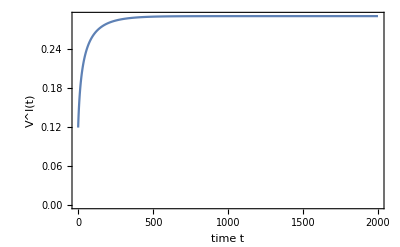

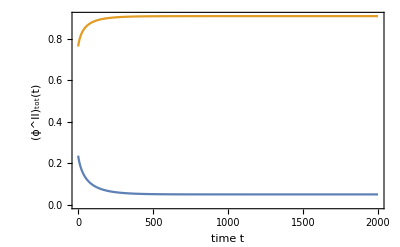

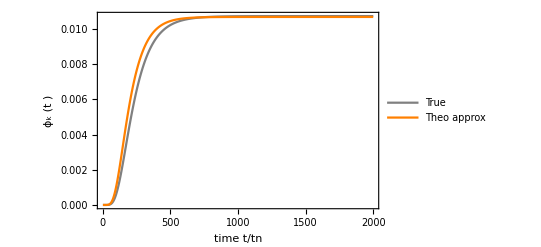

```mathematica
ListLinePlot[ VIArr , PlotRange->All ,  Frame->True, FrameLabel->{"time t", "V^I(t)"}]

phitI = Table[ Sum[phiIArr[[i,j]], {j,1,M}],{i,1,Length[phiIArr]}];
phitII = Table[ Sum[phiIIArr[[i,j]], {j,1,M}],{i,1,Length[phiIArr]}];
pltot = ListLinePlot[  {phitII, phitI}, PlotRange->All , Frame->True, FrameLabel->{"time t", "(ϕ^II)_tot(t)"}]


bet = (1+2 phi/ϕSt-√(1+4 phi/ϕSt))/(2 phi/ϕSt);
alp = 1/bet;

at = (1-E^(-(alp - bet)ntime*dt*phi))/(alp -bet E^(-(alp - bet)ntime*dt*phi));

ktest = 10;
pltest = ListPlot[  phiIArr[[;;,ktest]], PlotRange->All] ;
pkTheo = Table[( ktest(1-at)^2 at^(ktest-1) phi )/.phi->phitI[[ntime+1]],{ntime,0,nIter-2}];
pltestTheo = ListLinePlot[ {phiIArr[[;;,ktest]], pkTheo} ,PlotStyle->{Gray, Orange},PlotLegends->{"True", "Theo approx"},PlotRange->All, Frame->True, FrameLabel->{"time t/tn", " ϕ_k (t )"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["results/kinetics/classI/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pHomo_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[pHomo[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classI/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pAver_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiAverArr[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classI/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pI_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiIArr[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classI/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pII_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiIIArr[[;;,1;;M]]], -nIter]];
Export["results/kinetics/classI/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/VI_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[VIArr], -nIter]];
```

```mathematica
(*meanNhomo = Table[ Sum[nHomo[[i,k]]*molVol[[k]],{k,1,M}]/Sum[nHomo[[i,k]],{k,1,M}],{i,1,nIter}];
meanN = Table[ Sum[nAverArr[[i,k]]*molVol[[k]],{k,1,M}]/Sum[nAverArr[[i,k]],{k,1,M}],{i,1,nIter}];
p1 = ListLinePlot[ {meanNhomo, meanN} , PlotStyle->{Blue,Red}, PlotLegends->{"Homo","Drop"}]
p2 = ListLinePlot[ {meanNhomo, meanN} , PlotStyle->{Blue,Red}, PlotLegends->{"Homo","Drop"}, PlotRange->{{1,5},{0.9,1.2}}]*)
```

## Class II

```mathematica
M=18;
r=1;

phit=0.2;
(*phit=0.5;*)
(*phit=0.35;*)

kT=0.35;

eInt= -1;
sInt=-2.; 

d=1;

dt= 0.002;
nIter = 20000;

χ = 1/kT;

χp=0.2/kT;
delχ = χ-χp;
```

```mathematica
(*delrChem is a M vector, with i-th component containing the fluxes from the i to the i+1 assembly associated to the single reactions. The last element is set to 0, since there is no flux to M+1 mers*)

(* USEFUL FOR GENERIC DIMENSION, CLASS I *)
(* w = Join[Table[-(eInt/kT-sInt)/i^(1/d),{i,1,M}],{0} ];
delrChem = Join[Table[  (phi[i]*phi[1])/i *Exp[1-((i+1)*w[[i+1]]-i*w[[i]]-w[[1]] )]-phi[i+1]/(i+1),{i,1,M-1}]  ,{0}];*)

(* d=1, class 1 *)
ϕSt = E^(eInt/kT-sInt - 1- delχ phi[M+1]);
delrChem = Join[Table[Table[  2(phi[i]*phi[j])/(i*j)-2 phi[i+j]/(i+j) ϕSt,{j,1,M-1}]  ,{i,1,M-1}],{0}];
rChem = Join[ Table[i (1/2 Sum[delrChem[[j,i-j]],{j,1,i-1}] - Sum[delrChem[[i,j]],{j,1,M-i}]),{i,1,M}],{0}];
```

```mathematica
phidot = Table[ rChem[[i]]-j[i]+phi[i]Sum[  j[k], {k,1,M+1}], {i,1,M+1}];

(*Sgam = (1 +delχ phi[M+1]) Sum[ phi[i]/i,{i,1,M}]+ phi[M+1] + χp phi[M+1](1- phi[M+1]);*)
gami = Table[  Exp[  delχ  phi[M+1] + i( χp (phi[M+1])^2 - (1 +delχ phi[M+1])*Sum[ phi[k]/k,{k,1,M} ]- phi[M+1]) ],{i,1,M}];
gamM1 =  Exp[    χp (1- phi[M+1])^2 -phi[M+1]+ (delχ (1-phi[M+1]) -1 ) *Sum[ phi[k]/k,{k,1,M} ] ];
gam = Simplify[Join[gami,{gamM1}]];


phidot = Table[ rChem[[i]]-j[i]+phi[i]Sum[  j[k], {k,1,M+1}], {i,1,M+1}];

eqForj =Table[  gam [[i]]* phidot[[i]] +phi[i] Sum[D[gam[[i]],phi[k] ]*phidot[[k]] ,{ k,1,M+1}] ,{i,1,M+1}];
```

```mathematica
pAver = Join[{phit},Table[0,{i,1,M-1}],{1-phit}];

pHomo = {pAver};

For[k=0,k<nIter-1,k++,

incre = rChem/.Table[phi[i]->pAver[[i]],{i,1,M+1}];
(*Print[Sum[incre[[i]]*i,{i,1,M+1}]];*)
pAver = pAver+ dt* incre;
AppendTo[pHomo,pAver] ;

]
```

This should be 1

1.

-Graphics-

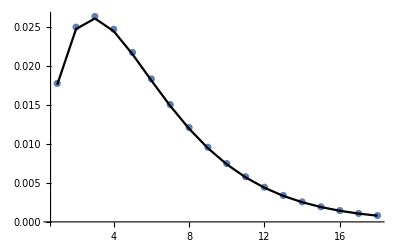

```mathematica
pHomoFinal = pHomo[[-1]];

Print["This should be 1"]
Sum[pHomoFinal[[i]],{i,1,M+1}]
pHomo = (MatrixForm[pHomo])[[1]] ;

SetDirectory[NotebookDirectory[]];
pnHomoEq=Flatten[Import["results/stat_states/classII_pn_homo.csv"]];
plHomo = ListPlot[  Table[ Table[{j,pHomo[[i,j]]},{i,2,Length[pHomo]} ],{j,1,M}], PlotRange->All ];
plHomoLast = ListPlot[  Table[ {j,pHomo[[-1,j]]},{j,1,M}], PlotRange->All ];
plHomoEq = ListLinePlot[  pnHomoEq, PlotRange->All , PlotStyle->Black];
Show[plHomo, plHomoEq]
Show[plHomoLast, plHomoEq]
```

```mathematica
f1=phi Log[phi] + (1- phi)  Log[1-  phi] + χ*phi (1-phi);

mu1 = D[f1,phi];
osmP1 = Simplify[f1 -   D[freeM,phi]*phi];

eqs1={  (mu1/.phi->pI)==(mu1/.phi->pII ), (osmP1/.phi->pI)==(osmP1/.phi->pII )};

dilGuess = 0.1;
initial={{pI,1-dilGuess},{pII,dilGuess}};

sol1 = FindRoot[eqs1,initial];


phiI0 =Join[ {pI/.sol1}, Table[0,{i,1,M-1}],{1-pI/.sol1} ]
phiII0 =Join[ {pII/.sol1}, Table[0,{i,1,M-1}],{1-pII/.sol1} ]
VI0=( phit-(pII/.sol1))/((pI/.sol1)-(pII/.sol1))
```

{0.914317,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0856826}

{0.0856826,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.914317}

0.137959

```mathematica
phiIArr = {phiI0};
phiIIArr = {phiII0};
VIArr = {VI0} ;

phiI =phiI0;
phiII =phiII0;
x =VI0;

For[k=0,k<nIter-1,k++,

repI = Table[phi[i]->phiI[[i]],{i,1,M+1}];
repII = Join[Table[phi[i]->phiII[[i]],{i,1,M+1}],Table[j[i]->j[i]/(1-1/x),{i,1,M+1}]];
eqs = Table[(eqForj[[i]]/.repI)-(eqForj[[i]]/.repII)==0 ,{i,1,M+1}];


(*jsolRoot = Solve[eqs,Table[j[i],{i,1,M+1}]][[1]];
repSol = Table[j[i]->(j[i]/.jsolRoot), {i,1,M+1}];*)
coef = Normal[CoefficientArrays[eqs,Table[j[i],{i,1,M+1}]]];
const = -coef[[1]];
equaMat = coef[[2]];
jsol=LinearSolve[equaMat, const];
repSol = Table[j[i]->(jsol[[i]]), {i,1,M+1}];

increI = phidot/.repI/.repSol;
increII = phidot/.repII/.repSol;
increx = (-x * Sum[j[i],{i,1,M+1}])/.repSol;

phiI = phiI+ dt* increI;
AppendTo[phiIArr,phiI] ;

phiII = phiII+ dt* increII;
AppendTo[phiIIArr,phiII] ;

x = x+ dt*increx;
AppendTo[VIArr,x] ;

]
```

NO NEGATIVE NUMBERS

This should be 1: 1.

This should be 1: 1.

INSIDE

-Graphics-

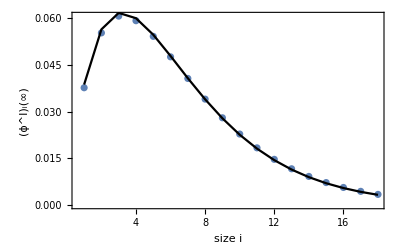

OUTSIDE

-Graphics-

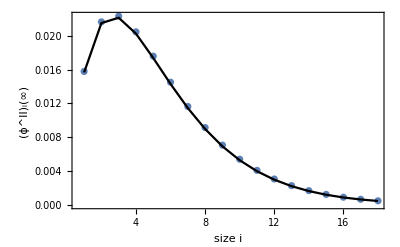

```mathematica
phiIArr = (MatrixForm[phiIArr])[[1]] ;
phiIIArr = (MatrixForm[phiIIArr])[[1]]; 
phiAverArr = Table[phiIIArr[[i]]*(1-VIArr[[i]])+ phiIArr[[i]]*VIArr[[i]],{i,1,Length[VIArr]}];
If[Min[phiIArr]<-10^-8|| Min[phiIIArr]<-10^-8|| Min[VIArr]<0,Print["AHI CARRAMBA"],Print["NO NEGATIVE NUMBERS "] ];

phiIfinal = phiIArr[[-1]];
Print["This should be 1: ", Sum[phiIfinal[[i]],{i,1,M+1}]];


phiIIfinal = phiIIArr[[-1]];
Print["This should be 1: ", Sum[phiIIfinal[[i]],{i,1,M+1}] ]

pnIIEq=Flatten[Import["results/stat_states/classII_pn_out.csv"]];
pnIEq=Flatten[Import["results/stat_states/classII_pn_in.csv"]];


plin = ListPlot[  Table[ Table[{j,phiIArr[[i,j]]},{i,2,Length[phiIArr]} ],{j,1,M}], PlotRange->All ];
plinLast = ListPlot[  phiIfinal[[;;-2]], PlotRange->All ];
plinEq = ListLinePlot[  pnIEq, PlotRange->All , PlotStyle->Black];

Print["INSIDE"]
Show[plin, plinEq,Frame->True, FrameLabel->{"size i", "(ϕ^I)_i(t)"}]
Show[plinLast,plinEq, Frame->True,  FrameLabel->{"size i", "(ϕ^I)_i(∞)"}]

plout=ListPlot[  Table[ Table[{j,phiIIArr[[i,j]]},{i,2,Length[phiIIArr]} ],{j,1,M}], PlotRange->All ];
ploutLast = ListPlot[  phiIIfinal[[;;-2]], PlotRange->All ];
ploutEq = ListLinePlot[  pnIIEq, PlotRange->All , PlotStyle->Black];

Print["OUTSIDE"]
Show[plout, ploutEq, Frame->True, FrameLabel->{"size i", "(ϕ^II)_i(t)"}]
Show[ploutLast,ploutEq,  Frame->True, FrameLabel->{"size i", "(ϕ^II)_i(∞)"}]
```

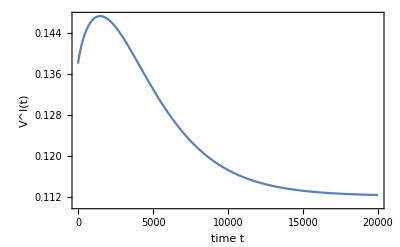

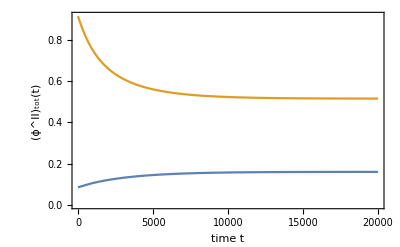

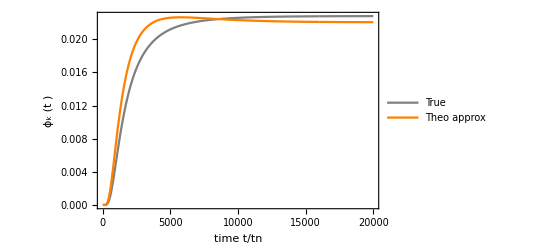

```mathematica
ListLinePlot[ VIArr , PlotRange->All ,  Frame->True, FrameLabel->{"time t", "V^I(t)"}]

phitI = Table[ Sum[phiIArr[[i,j]], {j,1,M}],{i,1,Length[phiIArr]}];
phitII = Table[ Sum[phiIIArr[[i,j]], {j,1,M}],{i,1,Length[phiIArr]}];
pltot = ListLinePlot[  {phitII, phitI}, PlotRange->All , Frame->True, FrameLabel->{"time t", "(ϕ^II)_tot(t)"}]

bet = (1+2 phi/ϕSt-√(1+4 phi/ϕSt))/(2 phi/ϕSt);
alp = 1/bet;

at = (1-E^(-(alp - bet)ntime*dt*phi))/(alp -bet E^(-(alp - bet)ntime*dt*phi));

ktest = 10;
pltest = ListPlot[  phiIArr[[;;,ktest]], PlotRange->All] ;
pkTheo = Table[( ktest(1-at)^2 at^(ktest-1) phi )/.{phi->phitI[[ntime+1]], phi[M+1]->1-phitI[[ntime+1]]},{ntime,0,nIter-2}];
pltestTheo = ListLinePlot[ {phiIArr[[;;,ktest]], pkTheo} ,PlotStyle->{Gray, Orange},PlotLegends->{"True", "Theo approx"},PlotRange->All, Frame->True, FrameLabel->{"time t/tn", " ϕ_k (t )"}]

(*Show[pltest, pltestTheo, Frame->True, FrameLabel->{"time t/tn", " ϕ_k (t )"}]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["results/kinetics/classII/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pHomo_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[pHomo[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classII/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pAver_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiAverArr[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classII/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pI_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiIArr[[;;,1;;M]]], -nIter] ];
Export["results/kinetics/classII/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/pII_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[phiIIArr[[;;,1;;M]]], -nIter]];
Export["results/kinetics/classII/M_"<>ToString[M]<>"_pt_"<>ToString[phit]<>"/VI_T_"<>ToString[kT]<>"_eInt"<>ToString[eInt]<>"_sInt"<>ToString[sInt]<>".csv",Take[Re[VIArr], -nIter]];
```

```mathematica
phiIArr
```